# Numerical methods for ⅈ u_t+1/2 u_xx+|u|^2 u=0 on a<x<b with periodic BC.

## Method of Lines

We need to define the points at which we are going to approximate solutions.   We need to approximate the pieces in the PDE we want to solve using these values.

```mathematica
Clear[D2s,D1c,D1f,D1b,D2w,Δx,n]
D2s[Δx_,n_]:=Δx^-2*SparseArray[{
Band[{1,1}]->-2.0,
Band[{1,2}]->1.0,
Band[{2,1}]->1.0,
{1,n}->1.0,{n,1}->1.0},{n,n}];
D1c[Δx_,n_]:=(2 Δx)^-1 SparseArray[{
Band[{2,1}]->-1.0,
Band[{1,2}]->1.0,
{1,n}->-1.0,{n,1}->1.0},{n,n}];
D1f[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->-1.0,
Band[{2,1}]->1.0,
{1,n}->1.0},{n,n}];
D1b[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->1.0,
Band[{1,2}]->-1.0,
{n,1}->-1.0},{n,n}];
D2w[Δx_,n_]:=(12 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,
Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,
Band[{3,1}]->-1.0,
Band[{1,n}]->16.0,
Band[{n,1}]->16.0,
Band[{1,n-1}]->-1.0,
Band[{n-1,1}]->-1.0
},{n,n}];
D2v[Δx_,n_]:=(180 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-490.0,
Band[{1,2}]->270.0,
Band[{2,1}]->270.0,
Band[{1,3}]->-27.0,
Band[{3,1}]->-27.0,
Band[{1,4}]->2.0,
Band[{4,1}]->2.0,
Band[{1,n}]->270.0,
Band[{n,1}]->270.0,
Band[{1,n-1}]->-27.0,
Band[{n-1,1}]->-27.0,
Band[{1,n-2}]->2.0,
Band[{n-2,1}]->2.0
},{n,n}];
n=10;
TabView[{
"D2s"->MatrixForm[D2s[Δx,n]],
"D1c"->MatrixForm[D1c[Δx,n]],
"D1f"->MatrixForm[D1f[Δx,n]],
"D1b"->MatrixForm[D1b[Δx,n]],
"D2w"->MatrixForm[D2w[Δx,n]],
"D2v"->MatrixForm[D2v[Δx,n]]
}]
```

123456

```mathematica
L=12;
{a,b}={-L,L};
n=123;
Δx=2.0 L/n;
D2c=Δx^-2*SparseArray[{
Band[{1,1}]->-2.0,
Band[{1,2}]->1.0,
Band[{2,1}]->1.0,
{1,n}->1.0,{n,1}->1.0},{n,n}];
D1c=(2 Δx)^-1 SparseArray[{
Band[{2,1}]->-1.0,
Band[{1,2}]->1.0,
{1,n}->-1.0,{n,1}->1.0},{n,n}];
D1f=(Δx)^-1 SparseArray[{
Band[{1,1}]->-1.0,
Band[{2,1}]->1.0,
{1,n}->1.0},{n,n}];
D1b=(Δx)^-1 SparseArray[{
Band[{1,1}]->1.0,
Band[{1,2}]->-1.0,
{n,1}->-1.0},{n,n}];
D2w=(12Δx)^-2*SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,
Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,
Band[{3,1}]->-1.0,
{1,n}->1.0,{n,1}->1.0},{n,n}];

x[j_]:= a+ Δx j
f[x_]:=1.2 Sin[3 π x/L]-0.4 Cos[2 π x/L]+3.2Sin[5 π x/L]
fVec=Table[f[x[j]],{j,1,n}];
D1fVec=Table[f'[x[j]],{j,1,n}];
D2fVec=Table[f''[x[j]],{j,1,n}];
TabView[{
"f"->Show[Plot[f[x],{x,a,b},PlotStyle->Red],
ListPlot[fVec,DataRange->{a+Δx,b}]],
"f'"->Show[Plot[f'[x],{x,a,b},PlotStyle->Red],
ListPlot[D1c.fVec,DataRange->{a+Δx,b}]],
"f''"->Show[Plot[f''[x],{x,a,b},PlotStyle->Red],
ListPlot[D2.fVec,DataRange->{a+Δx,b}]],
"|f'-D_(1?).f|" -> ListLogPlot[ {D1fVec-D1f.fVec,D1fVec-D1b.fVec,D1fVec-D1c.fVec},
DataRange->{-L,L},PlotLegends->{"f","b","c"},GridLines->Automatic],
"|f''-D_(2?).f|" -> ListLogPlot[ Abs[D2fVec-D2c.fVec],
DataRange->{-L,L},PlotLegends->{"c","w","vw"},GridLines->Automatic]
}]
```

We need to define and check our approximate differentiation matrices.

We need to understand how to incorporate periodic boundary conditions.

We need to understand (in as many ways as possible) the effects of our different approximate differentiation matrices.

## Spectral Methods

We need to understand and check the Fourier solvers for linear PDEs.  The first thing we need to understand is the order that our FFT puts the pieces in.   We decided we are doing a periodic problem on the interval -L<x<L.  We are going to assume our data is of length n with x_1=-L+Δx, x_2=-L+2 Δx, and x_n=-L+n Δx=L

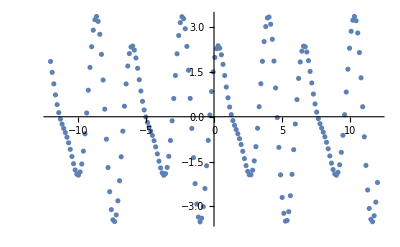

```mathematica
L=12;
n=200;
Δx=2.0L/n;
f[x_]:= 1.2 Cos[3x]+2.4 Sin[2x]+ 0.3 Cos[2x]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
ListPlot[fVec,DataRange->{-L,L}]
```